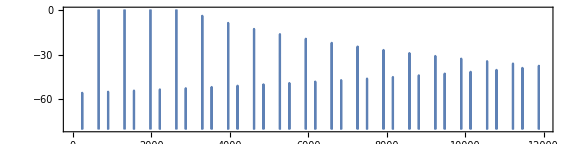

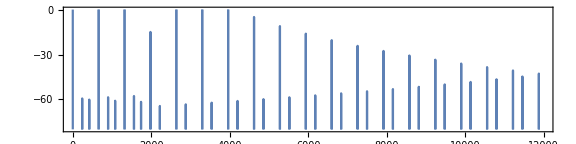

-Graphics-

```mathematica
sr=24000;t=1/sr;
fb=660;
fmod=fb 3; (* 1/2^n octave divider *)
nHarms=Floor[sr/fb];
harms=Range[fb,nHarms*fb,fb]//N;
ampls=Range[nHarms]^-3//N;
hAs=MapThread[List,{ampls,harms}];
a=Table[Sum[x[[1]]Sin[x[[2]] n 2Pi],{x,hAs}],{n,0,1-t,t}]//N;
m=Table[Sin[fmod n 2 Pi],{n,0,1-t,t}]//N;
Periodogram[a,SampleRate->sr,Frame->True,PlotRange->{Automatic,{-80,0}},AspectRatio->1/4,ImageSize->Large]
Periodogram[a*m,SampleRate->sr,Frame->True,PlotRange->{Automatic,{-80,0}},AspectRatio->1/4,ImageSize->Large]
ListPlay[a+a*m,SampleRate->sr]
```

```mathematica
sr=24000;t=1/sr;
d=2^(1/12)//N; (* chromatic scale note distance *)
fb=440;
fmod=fb 2;
keys={1,3,5,7,9,12,24,32,15,17,19,23};
notes=Table[fb d^RandomChoice[keys],12];
nn=Length[notes];
a=Table[Sin[notes[[Floor[4n]+1]] n 2Pi],{n,0,nn/4-t,t}]//N;
m=Table[Sin[fmod n 2 Pi],{n,0,nn/4-t,t}]//N;
m2=Table[Sin[fmod 1/4 n 2 Pi],{n,0,nn/4-t,t}]//N;
m3=Table[Sin[fmod 1/2 n 2 Pi],{n,0,nn/4-t,t}]//N;
ListPlay[a*m*m2*m3,SampleRate->sr]
```

-Graphics-

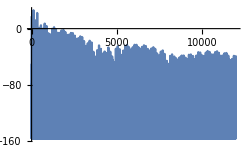

-Graphics-

```mathematica
sr=24000;t=1/sr;
fb=110;
fmod=2fb;
(* clipping function as waveshaper *)
ws[x_,c_]:=If[Abs[x]>c,Sign[x]c,x];
ws2[x_,c_]:=Sign[x]Sqrt[x]
a=Table[1-2SawtoothWave[t fb],{t,0,1-t,t}];
m=Table[Sin[t fmod 2Pi],{t,0,1-t,t}];
Periodogram[ws[#,0.3]&/@(a*m),SampleRate->sr]
ListPlay[a+a*m]
```

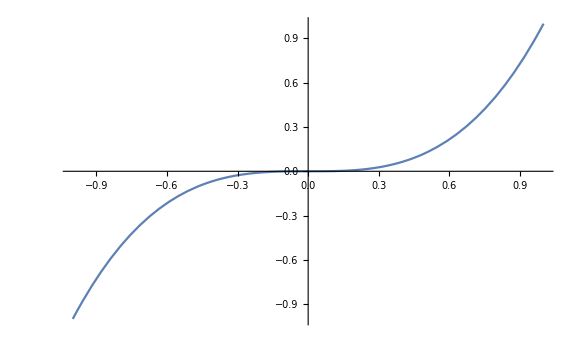

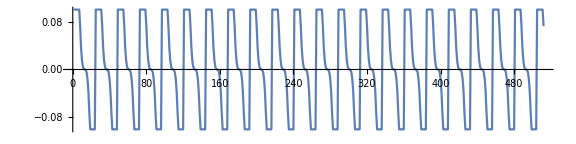

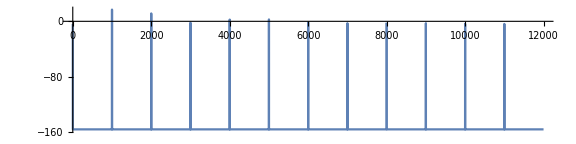

-Graphics-

```mathematica
sr=24000;t=1/sr;
fb=1000;
fmod=2fb;
ws2[x_]:=x*x^2;
Plot[ws2@x,{x,-1,1}]
a=Table[1-2SawtoothWave[t fb],{t,0,1-t,t}]//N;
aa=ws[#,0.1]&/@ws2/@a;
ListLinePlot[aa[[1;;512]],AspectRatio->1/4]
Periodogram[aa,SampleRate->sr,AspectRatio->1/4]
ListPlay[aa]
```